```mathematica
r=1
```

1

since we are taking r = 1 we can ignore r

```mathematica
b1[x_]:=1/(4x)
```

```mathematica
m1[x_]:= 0
```

```mathematica
d1[x_] := Sqrt[(1/4) * (1 + m1[x]m1[x])-b1[x]*b1[x]]
```

```mathematica
y1[x_] := (b1[x]-m1[x]*d1[x])/(1+m1[x]*m1[x])
```

```mathematica
x1[x_] := (-m1[x]b1[x]-d1[x])/(1+m1[x]*m1[x])
```

```mathematica
m2[x_] := (y1[x]-x)/x1[x]
```

```mathematica
b2[x_]:=y1[x]-m2[x]x1[x]
```

```mathematica
d2[x_] := Sqrt[(1+m2[x]*m2[x])-b2[x]*b2[x]]
```

```mathematica
y3[x_]:= (b2[x]-m2[x]d2[x])/(1+m2[x]*m2[x])
```

```mathematica
T1[x_]:= 2*(Pi - ArcCos[y3[x]])
```

```mathematica
P1[x_]:=T1[x]/(2Pi)
```

```mathematica
P1[x]
```

(π-ArcCos[(x+((1/(4 x)-x) √(1+(1/(4 x)-x)^2/(1/4-1/(16 x^2))-x^2))/(√(1/4-1/(16 x^2))))/(1+(1/(4 x)-x)^2/(1/4-1/(16 x^2)))])/π

```mathematica
y4[x_]:= (b2[x]+ m2[x]d2[x])/(1+m2[x]*m2[x])
```

```mathematica
T2[x_]:=2*ArcCos[y4[x]]
```

```mathematica
P2[x_]:=T2[x]/(2Pi)
```

```mathematica
P2[x]
```

ArcCos[(x-((1/(4 x)-x) √(1+(1/(4 x)-x)^2/(1/4-1/(16 x^2))-x^2))/(√(1/4-1/(16 x^2))))/(1+(1/(4 x)-x)^2/(1/4-1/(16 x^2)))]/π

```mathematica
P3[x_]:=Simplify[P1[x]+P2[x]]
```

```mathematica
P3[x]
```

(π-ArcCos[-(-1+√(-3+12 x^2))/(4 x)]+ArcCos[(1+√(-3+12 x^2))/(4 x)])/π

```mathematica
P3[0.500001]
```

0.998727

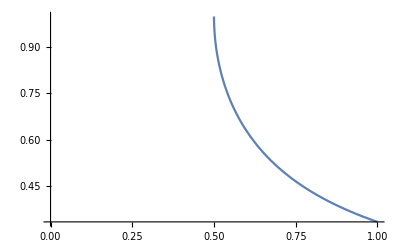

```mathematica
Plot[P3[x], {x, 0, 1}]
```

```mathematica
P[x_]:=If[x<=0.5, 1, P3[x]]
```

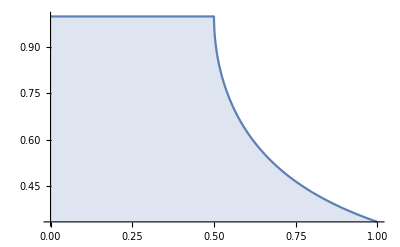

```mathematica
DiscretePlot[P[x], {x, 0, 1, 0.0001}]
```